# Contribution from Parallel Strategies for Spatial Orientation in C. elegans

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
n=93;
ColorData[n][1]
ColorData[n][2]
ColorData[n][3]
ColorData[n][4]
```

Hue[0, 0.8, 0.85]

Hue[0.11, 0.75, 0.92]

Hue[0.17, 0.6, 0.52]

Hue[0.06, 0.75, 0.92]

## Experiment 1: Replicating original results from the model

### Grid assay

#### 1A: Dt = 0.6

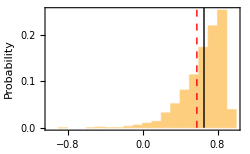

```mathematica
ci =Flatten[ Import["E1/exp1A_ci.csv"]];
Histogram[ci,15,"Probability",Frame->True,FrameLabel->{"Chemotaxis Index","Probability"},PlotRange->{{-1,1},Automatic},ImageSize->250,Epilog->{Directive[{Black,Thick}],Line[{{Mean[ci],0.0},{Mean[ci],1300}}],Directive[{Red,Thick,Dashed}],Line[{{0.58,0.0},{0.58,1300}}]}]
Export["1a_ci.eps",%];
```

```mathematica
Mean[ci]
```

0.656034000000000001

$Aborted

Part::partw: Part 2 of {} does not exist.

Table::iterb: Iterator {x,0,-1+{}⟦2⟧} does not have appropriate bounds.

Part::partd: Part specification d⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {Table[x dt,{x,0,-1+{}⟦2⟧}],d⟦1⟧} cannot be transposed.

Table::iterb: Iterator {x,0,-1+{}⟦2⟧} does not have appropriate bounds.

Part::partd: Part specification d⟦2⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {Table[x dt,{x,0,-1+{}⟦2⟧}],d⟦2⟧} cannot be transposed.

Table::iterb: Iterator {x,0,-1+{}⟦2⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Part::partd: Part specification d⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Table[x dt,{x,0,-1+{}⟦2⟧}],d⟦3⟧} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLinePlot::lpn: Transpose[{Table[x dt,{x,0.,-1.+{}⟦2⟧}],Mean[d]}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

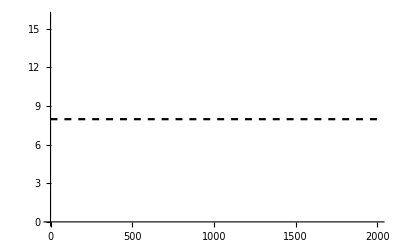
Show[{-Graphics-,ListLinePlot[Transpose[{Table[x dt,{x,0,-1+{}⟦2⟧}],Mean[d]}],PlotRange→All,PlotStyle→GrayLevel[0]],-Graphics-},Frame→True,FrameLabel→{Time (sec),Distance to closest peak (mm)},ImageSize→250]

Table::iterb: Iterator {x,0,-1+{}⟦2⟧} does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Table[x dt,{x,0,-1+{}⟦2⟧}],Mean[d]} cannot be transposed.

Table::iterb: Iterator {x,0,-1.+{}⟦2⟧} does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Table[x dt,{x,0,-1.+{}⟦2⟧}],Mean[d]} cannot be transposed.

Table::iterb: Iterator {x,0.,-1.+{}⟦2⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Table[x dt,{x,0.,-1.+{}⟦2⟧}],Mean[d]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLinePlot::lpn: Transpose[{Table[x dt,{x,0.,-1.+{}⟦2⟧}],Mean[d]}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

```mathematica
d = Import["E1/exp1A_d.csv"];
dt=0.6;
time=Table[x dt,{x,0,Dimensions[d][[2]]-1}];
Show[
{ListLinePlot[Table[Transpose[{time,d[[x]]}],{x,1,5}],PlotRange->All,PlotStyle->Opacity[0.5]],
ListLinePlot[Transpose[{time,Mean[d]}],PlotRange->All,PlotStyle->Black],
Plot[Sqrt[2/Pi] 10,{x,0,2000},PlotStyle->{Black,Dashed}]
},
Frame->True,
FrameLabel->{"Time (sec)","Distance to closest peak (mm)"},
ImageSize->250
]
Export["1a_d.eps",%];
```

#### 1B: Dt = 0.1

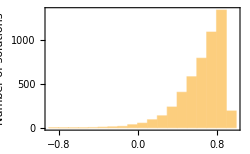

```mathematica
ci =Flatten[ Import["E1/exp1B_ci.csv"]];
Histogram[ci,15,Frame->True,FrameLabel->{"Chemotaxis Index","Number of solutions"},ImageSize->250]
```

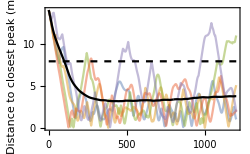

```mathematica
d = Import["E1/exp1B_d.csv"];
dt=0.1;
time=Table[x dt,{x,0,Dimensions[d][[2]]-1}];
Show[
{ListLinePlot[Table[Transpose[{time,d[[x]]}],{x,1,5}],PlotRange->All,PlotStyle->Opacity[0.5]],
ListLinePlot[Transpose[{time,Mean[d]}],PlotRange->All,PlotStyle->Black],
Plot[Sqrt[2/Pi] 10,{x,0,2000},PlotStyle->{Black,Dashed}]
},
Frame->True,
FrameLabel->{"Time (sec)","Distance to closest peak (mm)"},
ImageSize->250
]
```

#### 1C: Dt=0.6, No strategy

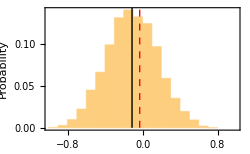

```mathematica
ci =Flatten[ Import["E1/exp1C_ci.csv"]];
Histogram[ci,15,"Probability",Frame->True,FrameLabel->{"Chemotaxis Index","Probability"},PlotRange->{{-1,1},Automatic},ImageSize->250,Epilog->{Directive[{Black,Thick}],Line[{{Mean[ci],0.0},{Mean[ci],1300}}],Directive[{Red,Thick,Dashed}],Line[{{-0.03,0.0},{-0.03,1300}}]}]
Export["1c_ci.eps",%];
```

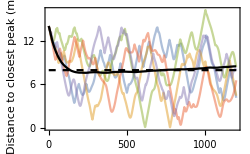

```mathematica
d = Import["E1/exp1C_d.csv"];
dt=0.6;
time=Table[x dt,{x,0,Dimensions[d][[2]]-1}];
Show[
{ListLinePlot[Table[Transpose[{time,d[[x]]}],{x,1,5}],PlotRange->All,PlotStyle->Opacity[0.5]],
ListLinePlot[Transpose[{time,Mean[d]}],PlotRange->All,PlotStyle->Black],
Plot[Sqrt[2/Pi] 10,{x,0,2000},PlotStyle->{Black,Dashed}]
},
Frame->True,
FrameLabel->{"Time (sec)","Distance to closest peak (mm)"},
ImageSize->250
]
Export["1c_d.eps",%];
```

### Radial Assay

#### 1A_R: Dt=0.6, Dual

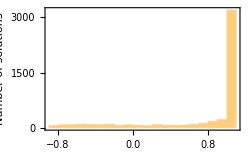

```mathematica
ci =Flatten[ Import["E1/exp1A2_R_ci.csv"]];
Histogram[ci,15,Frame->True,FrameLabel->{"Chemotaxis Index","Number of solutions"},ImageSize->250]
```

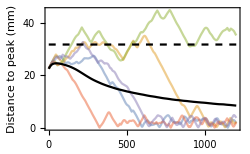

```mathematica
d = Import["E1/exp1A2_R_d.csv"];
dt=0.6;
time=Table[x dt,{x,0,Dimensions[d][[2]]-1}];
Show[
{ListLinePlot[Table[Transpose[{time,d[[x]]}],{x,1,5}],PlotRange->All,PlotStyle->Opacity[0.5]],
ListLinePlot[Transpose[{time,Mean[d]}],PlotRange->All,PlotStyle->Black],
Plot[Sqrt[(45^2)/2] ,{x,0,2000},PlotStyle->{Black,Dashed}]
},
Frame->True,
FrameLabel->{"Time (sec)","Distance to peak (mm)"},
ImageSize->250
]
```

#### 1C_R: Dt=0.6, No strategy

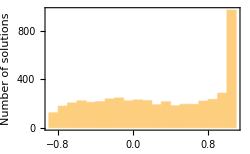

```mathematica
ci =Flatten[ Import["E1/exp1C2_R_ci.csv"]];
Histogram[ci,15,Frame->True,FrameLabel->{"Chemotaxis Index","Number of solutions"},ImageSize->250]
```

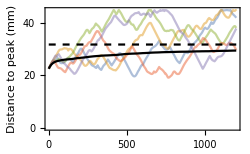

```mathematica
d = Import["E1/exp1C2_R_d.csv"];
dt=0.6;
time=Table[x dt,{x,0,Dimensions[d][[2]]-1}];
Show[
{ListLinePlot[Table[Transpose[{time,d[[x]]}],{x,1,5}],PlotRange->All,PlotStyle->Opacity[0.5]],
ListLinePlot[Transpose[{time,Mean[d]}],PlotRange->All,PlotStyle->Black],
Plot[Sqrt[(45^2)/2] ,{x,0,2000},PlotStyle->{Black,Dashed}]
},
Frame->True,
FrameLabel->{"Time (sec)","Distance to peak (mm)"},
ImageSize->250
]
```

## Experiment 2: Effect of noise and pirouette window

Grid assay. 
dt = 0.1. 
Dual. 
Reps = 5000. 
Noise = np.linspace (0, 0.02, conds)

### 2A: Using v1 of pirouette window integration

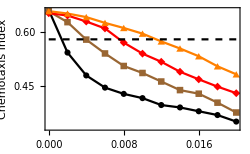

```mathematica
m=0.02;
noiseaxis = Table[x,{x,0,m,m/10}];
ci1 = Mean[Import["E2/exp2_0.1_ci.csv"]];
ci2 = Mean[Import["E2/exp2_0.3_ci.csv"]];
ci3 = Mean[Import["E2/exp2_0.6_ci.csv"]];
ci4 = Mean[Import["E2/exp2_1.2_ci.csv"]];
Show[
{
ListLinePlot[{Transpose[{noiseaxis,ci1}],Transpose[{noiseaxis,ci2}],Transpose[{noiseaxis,ci3}],Transpose[{noiseaxis,ci4}]},PlotStyle->{Black,Brown,Red,Orange},PlotMarkers->Automatic],
Plot[0.58,{x,0,0.2},PlotStyle->{Black,Dashed}]
},
Frame->True,
FrameLabel->{"Noise Std.","Chemotaxis Index"},
ImageSize->250]
Export["2a_ci.eps",%];
```

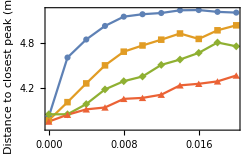

```mathematica
m=0.02;
noiseaxis = Table[x,{x,0,m,m/10}];
ci1 = Mean[Import["E2/exp2_0.1_d.csv"]];
ci2 = Mean[Import["E2/exp2_0.3_d.csv"]];
ci3 = Mean[Import["E2/exp2_0.6_d.csv"]];
ci4 = Mean[Import["E2/exp2_1.2_d.csv"]];
ListLinePlot[{Transpose[{noiseaxis,ci1}],Transpose[{noiseaxis,ci2}],Transpose[{noiseaxis,ci3}],Transpose[{noiseaxis,ci4}]},PlotMarkers->Automatic,
Frame->True,
FrameLabel->{"Noise Std.","Distance to closest peak (mm)"},
ImageSize->250]
Export["2a_d.eps",%];
```

### 2B: Using v2 of pirouette window integration

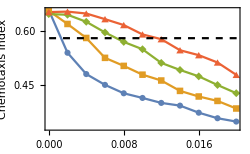

```mathematica
m=0.02;
noiseaxis = Table[x,{x,0,m,m/10}];
ci1 = Mean[Import["E2/exp2b_0.1_ci.csv"]];
ci2 = Mean[Import["E2/exp2b_0.3_ci.csv"]];
ci3 = Mean[Import["E2/exp2b_0.6_ci.csv"]];
ci4 = Mean[Import["E2/exp2b_1.2_ci.csv"]];
Show[
{
ListLinePlot[{Transpose[{noiseaxis,ci1}],Transpose[{noiseaxis,ci2}],Transpose[{noiseaxis,ci3}],Transpose[{noiseaxis,ci4}]},PlotMarkers->Automatic],
Plot[0.58,{x,0,2000},PlotStyle->{Black,Dashed}]
},
Frame->True,
FrameLabel->{"Noise Std.","Chemotaxis index"},
ImageSize->250]
Export["2b_ci.eps",%];
```

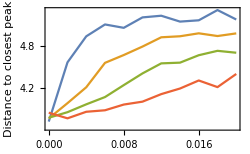

```mathematica
m=0.02;
noiseaxis = Table[x,{x,0,m,m/10}];
ci1 = Mean[Import["E2/exp2b_0.1_d.csv"]];
ci2 = Mean[Import["E2/exp2b_0.3_d.csv"]];
ci3 = Mean[Import["E2/exp2b_0.6_d.csv"]];
ci4 = Mean[Import["E2/exp2b_1.2_d.csv"]];
ListLinePlot[{Transpose[{noiseaxis,ci1}],Transpose[{noiseaxis,ci2}],Transpose[{noiseaxis,ci3}],Transpose[{noiseaxis,ci4}]},
Frame->True,
FrameLabel->{"Noise Std.","Distance to closest peak"},
ImageSize->250]
Export["2b_d.eps",%];
```

## Experiment 4: Contributions from the different strategies within the Grid Assay with Noise 0.008 and Pir. Window 0.6

Grid assay. 
dt = 0.1. 
Reps = 5000. 
Noise = 0.008
steepness = 1.0
Show individual trajectories in a bird’s eye view for each strategy, in four plates.
Show the average distance to the peak over time for each strategy in one figure.
Show the histograms of the CI for each strategy in one figure.

### Plates

#### Dual

```mathematica
x1= Import["E4/exp4xy_dual_x.csv"];
y1= Import["E4/exp4xy_dual_y.csv"];
```

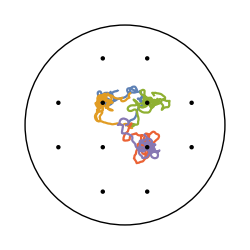

```mathematica
Show[
{
ListLinePlot[Table[Transpose[{x1[[x]],y1[[x]]}],{x,1,5}],Axes->False],
Graphics[Circle[{0.0,0.0},45]],
Graphics[Disk[{-30,10}]],
Graphics[Disk[{-30,-10}]],
Graphics[Disk[{-10,30}]],
Graphics[Disk[{-10,10}]],
Graphics[Disk[{-10,-10}]],
Graphics[Disk[{-10,-30}]],
Graphics[Disk[{10,30}]],
Graphics[Disk[{10,10}]],
Graphics[Disk[{10,-10}]],
Graphics[Disk[{10,-30}]],
Graphics[Disk[{30,10}]],
Graphics[Disk[{30,-10}]]
},
Frame->False,
PlotRange->{{-46,46},{-46,46}},
AspectRatio->True,
ImageSize->250
]
Export["3_dual.eps",%];
```

#### PR

```mathematica
x1= Import["E4/exp4xy_pr_x.csv"];
y1= Import["E4/exp4xy_pr_y.csv"];
```

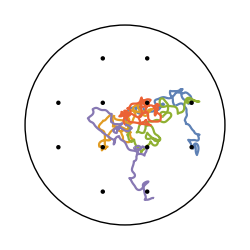

```mathematica
Show[
{
ListLinePlot[Table[Transpose[{x1[[x]],y1[[x]]}],{x,1,5}],Axes->False],
Graphics[Circle[{0.0,0.0},45]],
Graphics[Disk[{-30,10}]],
Graphics[Disk[{-30,-10}]],
Graphics[Disk[{-10,30}]],
Graphics[Disk[{-10,10}]],
Graphics[Disk[{-10,-10}]],
Graphics[Disk[{-10,-30}]],
Graphics[Disk[{10,30}]],
Graphics[Disk[{10,10}]],
Graphics[Disk[{10,-10}]],
Graphics[Disk[{10,-30}]],
Graphics[Disk[{30,10}]],
Graphics[Disk[{30,-10}]]
},
Frame->False,
PlotRange->{{-46,46},{-46,46}},
AspectRatio->True,
ImageSize->250
]
Export["3_pr.eps",%];
```

#### WV

```mathematica
x1= Import["E4/exp4xy_wv_x.csv"];
y1= Import["E4/exp4xy_wv_y.csv"];
```

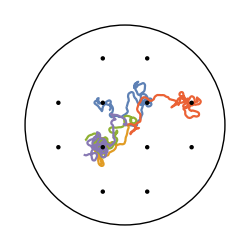

```mathematica
Show[
{
ListLinePlot[Table[Transpose[{x1[[x]],y1[[x]]}],{x,1,5}],Axes->False],
Graphics[Circle[{0.0,0.0},45]],
Graphics[Disk[{-30,10}]],
Graphics[Disk[{-30,-10}]],
Graphics[Disk[{-10,30}]],
Graphics[Disk[{-10,10}]],
Graphics[Disk[{-10,-10}]],
Graphics[Disk[{-10,-30}]],
Graphics[Disk[{10,30}]],
Graphics[Disk[{10,10}]],
Graphics[Disk[{10,-10}]],
Graphics[Disk[{10,-30}]],
Graphics[Disk[{30,10}]],
Graphics[Disk[{30,-10}]]
},
Frame->False,
PlotRange->{{-46,46},{-46,46}},
AspectRatio->True,
ImageSize->250
]
Export["3_wv.eps",%];
```

#### Null

```mathematica
x1= Import["E4/exp4xy_null_x.csv"];
y1= Import["E4/exp4xy_null_y.csv"];
```

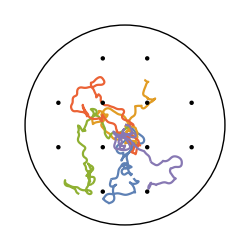

```mathematica
Show[
{
ListLinePlot[Table[Transpose[{x1[[x]],y1[[x]]}],{x,1,5}],Axes->False],
Graphics[Circle[{0.0,0.0},45]],
Graphics[Disk[{-30,10}]],
Graphics[Disk[{-30,-10}]],
Graphics[Disk[{-10,30}]],
Graphics[Disk[{-10,10}]],
Graphics[Disk[{-10,-10}]],
Graphics[Disk[{-10,-30}]],
Graphics[Disk[{10,30}]],
Graphics[Disk[{10,10}]],
Graphics[Disk[{10,-10}]],
Graphics[Disk[{10,-30}]],
Graphics[Disk[{30,10}]],
Graphics[Disk[{30,-10}]]
},
Frame->False,
PlotRange->{{-46,46},{-46,46}},
AspectRatio->True,
ImageSize->250
]
Export["3_null.eps",%];
```

### Distance

```mathematica
d1 = Import["E4/exp4_dual_d.csv"];
d2 = Import["E4/exp4_pr_d.csv"];
d3 = Import["E4/exp4_wv_d.csv"];
d4 = Import["E4/exp4_null_d.csv"];
```

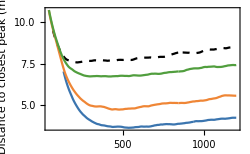

```mathematica
dt=0.1;
time=Table[x dt,{x,0,Dimensions[d1][[2]]-1}];
Show[
{ListLinePlot[Transpose[{time,Mean[d4]}],PlotStyle->{Black,Dashed}],
ListLinePlot[Transpose[{time,Mean[d1]}],PlotStyle->RGBColor["#3B75AF"]],
ListLinePlot[{Transpose[{time,Mean[d3]}],Transpose[{time,Mean[d2]}]},PlotStyle->{RGBColor["#EF8636"],RGBColor["#519E3E"]}]
},
PlotRange->All,
Axes->False,
Frame->True,
FrameLabel->{"Time (sec)","Distance to closest peak (mm)"},
ImageSize->250
]
Export["3_d.eps",%];
```

### Chemotaxis Index

```mathematica
c=ColorData[97,"ColorList"];
```

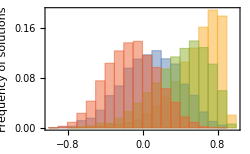

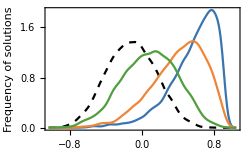

```mathematica
ci1=Flatten[ Import["E4/exp4_dual_ci.csv"]];
ci2=Flatten[ Import["E4/exp4_pr_ci.csv"]];
ci3=Flatten[ Import["E4/exp4_wv_ci.csv"]];
ci4=Flatten[ Import["E4/exp4_null_ci.csv"]];
Histogram[{ci1,ci2,ci3,ci4},Automatic,"Probability",Frame->True,FrameLabel->{"Chemotaxis Index","Frequency of solutions"},ImageSize->250]
SmoothHistogram[{ci4,ci1,ci3,ci2} ,Automatic,"PDF",Frame->True,Axes->False,PlotStyle->{Directive[Black,Dashed],RGBColor["#3B75AF"],RGBColor["#EF8636"],RGBColor["#519E3E"]},FrameLabel->{"Chemotaxis Index","Frequency of solutions"},ImageSize->250]
Export["3_ci.eps",%];
```

## Experiment 3: Contributions from the different strategies across steepness (without noise)

Grid assay. 
dt = 0.1. 
Reps = 5000. 
Noise = 0.008
steepness = np.linspace(0.1,1.9,conds)

### No noise

```mathematica
steepaxis = Table[x,{x,0.1,1.9,1.8/10}]
```

{0.1,0.28,0.46,0.64,0.82,1.,1.18,1.36,1.54,1.72,1.9}

```mathematica
ci1= Mean[Import["E3/exp3b_dual_ci.csv"]];
ci2= Mean[Import["E3/exp3b_pr_ci.csv"]];
ci3= Mean[Import["E3/exp3b_wv_ci.csv"]];
ci4 = Mean[Mean[Import["E3/exp3b_null_ci.csv"]]];
```

```mathematica
steepaxis[[3]]
(ci2[[3]]-ci4)/(ci1[[3]]-ci4)
(ci3[[3]]-ci4)/(ci1[[3]]-ci4)
steepaxis[[6]]
(ci2[[6]]-ci4)/(ci1[[6]]-ci4)
(ci3[[6]]-ci4)/(ci1[[6]]-ci4)
steepaxis[[9]]
(ci2[[9]]-ci4)/(ci1[[9]]-ci4)
(ci3[[9]]-ci4)/(ci1[[9]]-ci4)
```

0.46

0.365616

0.547031

1.

0.383406

0.694322

1.54

0.43783

0.846109

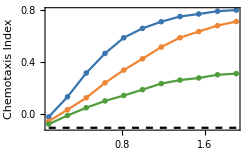

```mathematica
Show[
{
ListLinePlot[Transpose[{steepaxis,ci1}],PlotStyle->RGBColor["#3B75AF"],PlotMarkers->●],
ListLinePlot[{Transpose[{steepaxis,ci3}],Transpose[{steepaxis,ci2}]},PlotStyle->{RGBColor["#EF8636"],RGBColor["#519E3E"]},PlotMarkers->●],
Plot[ci4,{x,0.1,1.9},PlotStyle->{Black,Dashed}]
}
,
PlotRange->All,
Axes->False,
Frame->True,
FrameLabel->{"Scale","Chemotaxis Index"},
ImageSize->250
]
Export["4_ci.eps",%];
```

### No noise

```mathematica
steepaxis = Table[x,{x,0.1,1.9,1.8/10}];
```

```mathematica
ci1= Mean[Import["E3/exp3b_dual_d.csv"]];
ci2= Mean[Import["E3/exp3b_pr_d.csv"]];
ci3= Mean[Import["E3/exp3b_wv_d.csv"]];
ci4 = Mean[Mean[Import["E3/exp3b_null_d.csv"]]];
```

```mathematica
steepaxis[[3]]
(ci2[[3]]-ci4)/(ci1[[3]]-ci4)
(ci3[[3]]-ci4)/(ci1[[3]]-ci4)
steepaxis[[6]]
(ci2[[6]]-ci4)/(ci1[[6]]-ci4)
(ci3[[6]]-ci4)/(ci1[[6]]-ci4)
steepaxis[[9]]
(ci2[[9]]-ci4)/(ci1[[9]]-ci4)
(ci3[[9]]-ci4)/(ci1[[9]]-ci4)
```

0.46

0.2941189065467293

0.51552699363791166

1.

0.29631508353400781

0.60556400141853467

1.54

0.34902264040391281

0.77986696370309273

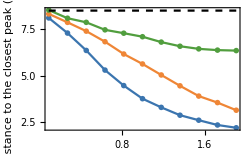

```mathematica
Show[
{
ListLinePlot[Transpose[{steepaxis,ci1}],PlotStyle->RGBColor["#3B75AF"],PlotMarkers->●],
ListLinePlot[{Transpose[{steepaxis,ci3}],Transpose[{steepaxis,ci2}]},PlotStyle->{RGBColor["#EF8636"],RGBColor["#519E3E"]},PlotMarkers->●],
Plot[ci4,{x,0.1,1.9},PlotStyle->{Black,Dashed}]
}
,
PlotRange->All,
Axes->False,
Frame->True,
FrameLabel->{"Scale","Distance to the closest peak (mm)"},
ImageSize->250
]
Export["4_d.eps",%];
```

### Noise

```mathematica
steepaxis = Table[x,{x,0.1,1.9,1.8/10}];
```

```mathematica
ci1x= Mean[Import["E3/exp3_dual_ci.csv"]];
ci2x= Mean[Import["E3/exp3_pr_ci.csv"]];
ci3x= Mean[Import["E3/exp3_wv_ci.csv"]];
ci4x = Mean[Mean[Import["E3/exp3_null_ci.csv"]]];
```

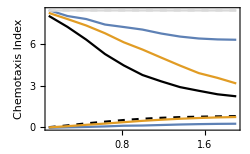

```mathematica
Show[
{
ListLinePlot[Transpose[{steepaxis,ci1}],PlotStyle->Black],
ListLinePlot[Transpose[{steepaxis,ci1x}],PlotStyle->{Black,Dashed}],
ListLinePlot[{Transpose[{steepaxis,ci2}],Transpose[{steepaxis,ci3}]}],
ListLinePlot[{Transpose[{steepaxis,ci2x}],Transpose[{steepaxis,ci3x}]}],
Plot[ci4,{x,0.1,1.9},PlotStyle->{LightGray}],
Plot[ci4,{x,0.1,1.9},PlotStyle->{LightGray,Dashed}]
}
,
PlotRange->All,
Axes->False,
Frame->True,
FrameLabel->{"Scale","Chemotaxis Index"},
ImageSize->250
]
```